# Numerical solver for hear curvature

## Definitions

### Find steady state

```mathematica
(*Define the 8 Gell-Mann Matrices (Generators of SU(3))*)
gm[1]={{0,1,0},{1,0,0},{0,0,0}};
gm[2]={{0,-I,0},{I,0,0},{0,0,0}};
gm[3]={{1,0,0},{0,-1,0},{0,0,0}};
gm[4]={{0,0,1},{0,0,0},{1,0,0}};
gm[5]={{0,0,-I},{0,0,0},{I,0,0}};
gm[6]={{0,0,0},{0,0,1},{0,1,0}};
gm[7]={{0,0,0},{0,0,-I},{0,I,0}};
gm[8]=1/Sqrt[3]*{{1,0,0},{0,1,0},{0,0,-2}};
id=IdentityMatrix[3];

(*Define a helper function for the Lindblad Dissipator*)
LindbladDissipator[L_,p_]:=L.p.ConjugateTranspose[L]-1/2*(ConjugateTranspose[L].L.p+p.ConjugateTranspose[L].L)

(*Define Bose-Einstein distribution*)
(*We set hbar=kB=1 for symbolic simplicity*)
nBE[omega_,T_]:=1/(Exp[omega/T]-1);

ClearAll[NumericalHeatCurvature];

NumericalHeatCurvature[hamFunc_,dissFunc_,params_,ranges_,points_:25]:=Module[{Htest,d,dSquared,basis,vec,unvec,solveResponse,p1Range,p2Range,step,data},(*1. Dynamically detect Hilbert space dimension*)Htest=hamFunc@@{ranges[[1,2]],ranges[[2,2]]};
d=Length[Htest];
dSquared=d^2;
(*2. Generalized Basis for d x d operators*)basis=Flatten[Table[ReplacePart[ConstantArray[0,{d,d}],{i,j}->1],{i,d},{j,d}],1];
vec[m_]:=Flatten[m];
unvec[v_]:=Partition[v,d];(*Matches the detected dimension*)(*3. Linear Response Solver*)solveResponse[Lmat_,rhsVec_]:=Module[{augmentedMat,augmentedRhs},augmentedMat=Lmat;
augmentedMat[[1]]=vec[IdentityMatrix[d]];
augmentedRhs=rhsVec;
augmentedRhs[[1]]=0;
LinearSolve[augmentedMat,augmentedRhs]];
(*4. Calculation Loop*)p1Range=Subdivide[ranges[[1,2]],ranges[[1,3]],points];
p2Range=Subdivide[ranges[[2,2]],ranges[[2,3]],points];
step=10^-5;
Print["Computing 6x6 Numerical Curvature Grid..."];
data=Table[Module[{H,Lmat,rhoVec,dH1,dH2,dLrho1,dLrho2,drho1,drho2,rho},H=hamFunc[p1,p2];
(*Generate Liouvillian Matrix for the full d^2 space*)Lmat=Table[vec[-I*(H.b-b.H)+dissFunc[b][p1,p2]],{b,basis}]//Transpose;
rhoVec=NullSpace[Lmat][[1]];
rho=unvec[rhoVec/Tr[unvec[rhoVec]]];
dH1=(hamFunc[p1+step,p2]-H)/step;
dH2=(hamFunc[p1,p2+step]-H)/step;
dLrho1=-vec[-I*(dH1.rho-rho.dH1)+(dissFunc[rho][p1+step,p2]-dissFunc[rho][p1,p2])/step];
dLrho2=-vec[-I*(dH2.rho-rho.dH2)+(dissFunc[rho][p1,p2+step]-dissFunc[rho][p1,p2])/step];
drho1=unvec[solveResponse[Lmat,dLrho1]];
drho2=unvec[solveResponse[Lmat,dLrho2]];
{p2,p1,Re@Tr[dH1.drho2-dH2.drho1]}],{p1,p1Range},{p2,p2Range}];
ListContourPlot[Flatten[data,1],InterpolationOrder->3,ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{params[[2]],params[[1]]},PlotLabel->"6x6 Spin-Motion Heat Curvature"]];
```

### Compare reversible and dissipative heat Q_diss=-∫dt g_ij dλ^i/dt dλ^j/dt

```mathematica
ClearAll[ComputeCycleHeats];

ComputeCycleHeats[hamFunc_,dissFunc_,params_,rules_,R_,offset_,tau_:2 Pi,points_:50]:=Module[{d,d2,basis,vec,unvec,solveLResponse,getNumericalData,path,dPath,tStep,stepSize,gridData,qGeo,qDiss},(*1. Dimension Detection& Vectorization Setup*)Module[{Htest=(hamFunc@@offset)/. rules},d=Length[Htest];
d2=d^2;];
basis=Flatten[Table[ReplacePart[ConstantArray[0,{d,d}],{i,j}->1],{i,d},{j,d}],1];
vec[m_]:=Flatten[m];
unvec[v_]:=Partition[v,d];
(*2. Linear Response Solver:Solves L(X)=target for X*)solveLResponse[Lmat_,targetVec_]:=Module[{augMat,augRhs},augMat=Lmat;
augMat[[1]]=vec[IdentityMatrix[d]];(*Trace constraint*)augRhs=targetVec;
augRhs[[1]]=0;
LinearSolve[augMat,augRhs]];
(*3. Point-wise Physics Calculator*)getNumericalData[tVal_]:=Module[{pVals,H,Lmat,rhoVec,rho,dH,dLrho,drho,Ai,gMetric,vel,step=10^-5},(*Current Path Parameters*)pVals={R*Cos[tVal]+offset[[1]],R*Sin[tVal]+offset[[2]]};
vel={-R*Sin[tVal],R*Cos[tVal]};(*d(path)/dt*)(*Local H and L*)H=(hamFunc@@pVals)/. rules;
Lmat=Table[vec[-I*(H.b-b.H)+(dissFunc[b]@@pVals)],{b,basis}]//Transpose/. rules;
(*Steady State*)rhoVec=NullSpace[Lmat][[1]];
rho=unvec[rhoVec/Tr[unvec[rhoVec]]];
(*Derivatives of rho via Response Equation:L(d_i rho)=-(d_i L)(rho)*)drho=Table[Module[{pStep,Hstep,LmatStep,dLrhoVec},pStep=pVals;pStep[[i]]+=step;
Hstep=(hamFunc@@pStep)/. rules;
LmatStep=Table[vec[-I*(Hstep.b-b.Hstep)+(dissFunc[b]@@pStep)],{b,basis}]//Transpose/. rules;
dLrhoVec=-((LmatStep.rhoVec)-(Lmat.rhoVec))/step;
unvec[solveLResponse[Lmat,dLrhoVec]]],{i,2}];
(*One-Form Ai=Tr[H.d_i rho]*)Ai=Table[Re@Tr[H.drho[[i]]],{i,2}];
(*Friction Metric g_ij=Tr[d_i rho.L^-1(d_j rho)]*)(*Note:solveLResponse acts as L^-1*)gMetric=Table[Re@Tr[drho[[i]].unvec[solveLResponse[Lmat,vec[drho[[j]]]]]],{i,2},{j,2}];
{Ai.vel,vel.gMetric.vel}];
(*4. Integration over the Cycle*)Print["Integrating cycle for d=",d," system..."];
gridData=Table[getNumericalData[t],{t,Subdivide[0,2 Pi,points]}];
(*Simple Trapezoidal Integration*)tStep=(2 Pi)/points;
qGeo=tStep*Total[gridData[[All,1]]];
qDiss=-(1/tau)*tStep*Total[gridData[[All,2]]];
(*Result Formatting*)Print["--- Numerical Cycle Results (τ = ",tau,"] ---"];
Print["Geometric Heat (Q_geo): ",qGeo];
Print["Dissipated Heat (Q_diss): ",qDiss];
Print["Net Heat: ",qGeo+qDiss];
{qGeo,qDiss}];
```

## Example: Motion-TLS coupled system

Computing 6x6 Numerical Curvature Grid...

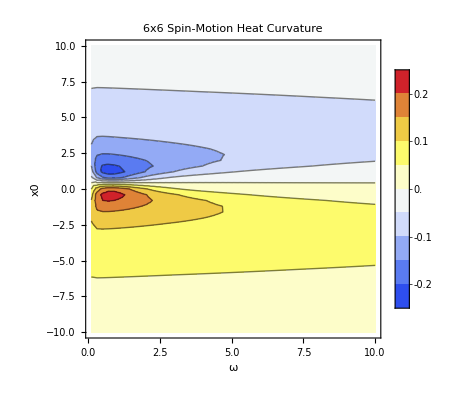

```mathematica
AnnihilationOp[n_]:=DiagonalMatrix[Sqrt[Range[n-1]],1];
Needs["Pauli`"];
Nmot = 2;
a=AnnihilationOp[Nmot];
adag=ConjugateTranspose[a];
mF =({{2, 0}, {0, 1}});
σup=(σ[1]+I*σ[2])/2;

(* Define the Hamiltonian *)
Htot[x0_,ω_]:=Module[{Δ=1,Ω=1,μB=1,dB=1,m=1},
xho= √(1/2m*ω);
η=(μB*xho*dB)/2;
Hmot = KroneckerProduct[σ[0],(ω*(adag.a)-ω*x0/xho*(adag+a))];
Hspin =KroneckerProduct[ (Δ*σ[3]+Ω*σ[1]),IdentityMatrix[Nmot]];
Hcoup =KroneckerProduct[mF,(η*(adag+a))];
Hmot+Hspin+Hcoup];

(* Define the dissipator *)
LOP[r_][γup_]:=LindbladDissipator[√γup*KroneckerProduct[σup,IdentityMatrix[Nmot]],r];
LDP[r_][γϕ_]:=LindbladDissipator[√(γϕ/2)*KroneckerProduct[σ[3],IdentityMatrix[Nmot]],r];
LC[r_][Γm_,n_]:=LindbladDissipator[√(Γm*(n+1))*KroneckerProduct[σ[0],a],r];
LH[r_][Γm_,n_]:=LindbladDissipator[√(Γm*n)*KroneckerProduct[σ[0],adag],r];

diss[r_][x0_,ω_]:=Module[{γup=1.0,γϕ=1.0,Γm=1.0,n=1.0},
LOP[r][γup]+LDP[r][γϕ]+LC[r][Γm,n]+LH[r][Γm,n]];

(* Heat curvature *)
NumericalHeatCurvature[Htot,diss,{x0,ω},{{x0,-10,10},{ω,0.1,10}},50 (*grid points*)]
```

```mathematica
results=ComputeCycleHeats[
Htot,(*The function Htot[x0,omega]*)
diss,(*The function diss[rho][x0,omega]*)
{x0,ω},{μB->1,dB->1,m->1,Δ->1,Ω->1},
0.9,(*Radius R*)
{1.0,1.0},(*Offset {x0_center,omega_center}*)
10.0,(*Period tau*)
40 (*Integration points*)];
```

Integrating cycle for d=6 system...

--- Numerical Cycle Results (τ = 10.] ---

Geometric Heat (Q_geo): 0.350292

Dissipated Heat (Q_diss): 0.00927666

Net Heat: 0.359568